```mathematica
(* Error phase approch for PDD, Magnus truncation vs full Matrix Log *)
```

```mathematica
{Id,X,Y,Z}=Table[σ[i]=PauliMatrix[i],{i,0,3}];
```

```mathematica
TrS[W_]:=Module[{n=Length[W]/2},Tr[Partition[W,{n,n}],Plus,2]];
TrB[ρ_]:=Map[Tr,Partition[ρ,{2,2}],{2}];
ProjB[W_]:=KroneckerProduct[Id/2,TrS[W]];
ProjSB[W_]:=W-ProjB[W];
BathOps[W_]:=Module[{Id=IdentityMatrix[Length[W]/2]},Table[TrS[W.KroneckerProduct[σ[i],Id]]/2,{i,1,3}]]
FromBathOps[B_List]:=Sum[KroneckerProduct[σ[i],B⟦i⟧],{i,1,3}];
ErrorPhase[W_]:=Norm[ProjSB[W]]
TcpNorm[W_]:=Norm/@{ProjB[W],ProjSB[W]};
FcpNorm[W_]:=Norm/@BathOps[W];
```

```mathematica
RandomCSqMat[n_]:=RandomVariate[NormalDistribution[],{n,n}]+ⅈ RandomVariate[NormalDistribution[],{n,n}]
RandomHermitian[n_]:=Module[{A=RandomCSqMat[n]},A+A†]
RandomUnitary[n_]:=Module[{A=RandomCSqMat[n]},Orthogonalize[A]]
RandomBath0[n_:2]:=Module[{A=RandomHermitian[n]},Normalize[A-(Tr[A]/n) IdentityMatrix[n],Norm]]
RandomBathOps[n_:2]:=Module[{W=Sum[KroneckerProduct[σ[i],RandomHermitian[n]],{i,1,3}]},BathOps[Normalize[W,Norm]]]
RandomOmega[a_,b_,n_:2]:=a KroneckerProduct[σ[0],RandomBath0[n]]+b Normalize[Sum[KroneckerProduct[σ[i],RandomHermitian[n]],{i,1,3}],Norm]
RandomUniRot[θ_]:=Module[{ϕ=RandomReal[2π],z=RandomReal[{-1,1}],x,y,c,s},
{x,y}=√(1-z^2){Cos[ϕ],Sin[ϕ]};
{c,s}={Cos[θ],Sin[θ]};
{{ c- ⅈ z*s,(-ⅈ x-y)*s},{(-ⅈ x+y)*s,c+ⅈ z*s}}]
```

```mathematica
(* Ideal case *)
cm[a_,b_]:=a.b-b.a
ac[a_,b_]:=a.b+b.a
PDD[U_]:=-KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U.KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U;
PDDn[U_,Z_,X_]:=-Z.U.X.U.Z.U.X.U;
Mag2BathOps[B0_,B_]:={-4ⅈ cm[B0,B⟦1⟧],-2ⅈ cm[B0,B⟦2⟧]-2 ac[B⟦1⟧,B⟦3⟧],0 B0};
```

```mathematica
RandPDDErPh[α_,β_]:=ErrorPhase[PDDMap[RandomOmega[α,β]]]
RandPDDErPhAp[α_,β_]:=Norm[FromBathOps[Mag2BathOps[α RandomBath0[],β RandomBathOps[]]]]
```

```mathematica
AbsoluteTiming[scanMagnusEP=Table[{α,β,
Mean[Table[Module[{B},
B[0]=α RandomBath0[];
{B[1],B[2],B[3]}=β RandomBathOps[];
ErrorPhase[PDDMap[Sum[KroneckerProduct[σ[i],B[i]],{i,0,3}]]]/ErrorPhase[FromBathOps[Mag2BathOps[B[0],{B[1],B[2],B[3]}]]]
],{10}]]},{α,0.01,1,0.01},{β,0.01,1,0.01}];]
```

{58.5799,Null}

```mathematica
Export[NotebookDirectory[]<>"scanMagnusEP.mx",scanMagnusEP];
```

```mathematica
MinMax[scanMagnusEP[[;;,;;,3]]]
```

{0.519301,83.7471}

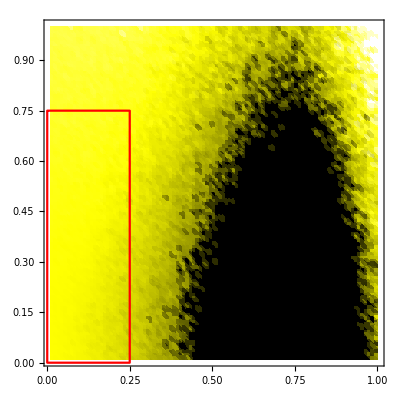

```mathematica
Show[ListDensityPlot[Flatten[scanMagnusEP,1],
ColorFunction->(Piecewise[{{Darker[Yellow,#-1],1≤#<1.5},{Lighter[Yellow,2(1-#)],0.8≤#<1},{White,0<#<1},{Black,1.5≤ #}}]&),
ColorFunctionScaling->False,PlotRange->All],
RegionPlot[{0<a<0.25&&0<b<0.75},{a,0,1},{b,0,1},PlotStyle->None,BoundaryStyle->Red]]
```

```mathematica
{αmax,βmax}={0.25,0.75};
{dα,dβ}={αmax,βmax}/100;
```

```mathematica
AbsoluteTiming[scaniPDDEPtest=ParallelTable[
ErrorPhase[MatrixLog[PDD[ MatrixExp[-ⅈ RandomOmega[α,β]] ]]]/β,{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
```

{2.01905,Null}

```mathematica
AbsoluteTiming[scaniPDDEP=ParallelTable[
{α,β,Max[Table[
ErrorPhase[PDDMap[RandomOmega[α,β]]]
,{1000}]]/β}
,{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}
];]
Export[NotebookDirectory[]<>"scaniPDDEP.mx",scaniPDDEP];
```

{1724.35,Null}

```mathematica
ConvergeBound[α_,β_]:=α+β<1/4
PDDBound1[α_,β_]:=12α+4β<1
PDDBound2[α_,β_]:=(0<β<√3 α&&α≤1/8)||(β>√3 α>0&&4 (10 α^2+(9 α^4)/β^2+β^2)≤1)
PDDBound3[α_,β_]:=(β/(√3)≤α≤1/8)|| (10 α^2+(9 α^4)/β^2+β^2)≤1/4
CDDBound3[α_,β_,n_]:=(β/(√(4^n-1))≤α≤1/2^(n+2))|| (((4^n-1)α^2+β^2)/(2α β))^2+1≤(1/(2^(n(n+1))α^n))^2
```

```mathematica
fpdd[x_]:=Piecewise[{{1,x<=√3},{1/2 √(1+(3/(2x)+x/2)^2),x>√3}}]
```

```mathematica
PDDBound2[α_,β_]:=(0<β<√3 α&&α≤1/8)||(β>√3 α>0&&4 (10 α^2+(9 α^4)/β^2+β^2)≤1)
PDDBound4[α_,β_]:=8α fpdd[β/α]≤1
```

```mathematica
fpdd[4.1]
```

2.61464

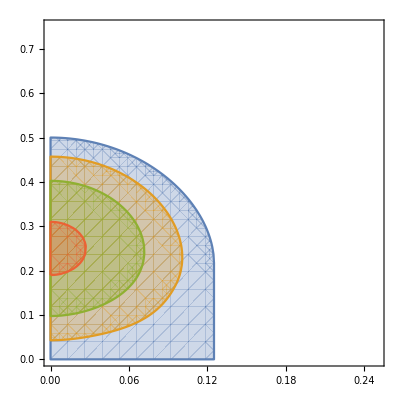

```mathematica
RegionPlot[ {
(8/π)(β-8α β fpdd[β/α])>=0,
(8/π)(β-8α β fpdd[β/α])>=0.1,
(8/π)(β-8α β fpdd[β/α])>=0.2,
(8/π)(β-8α β fpdd[β/α])>=0.3},
{α,0.0,0.25},{β,0.0,0.75}
]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
NumberForm[0.25 2/3,{2,2}]
```

0.17

```mathematica
0.25 1/3
```

0.0833333

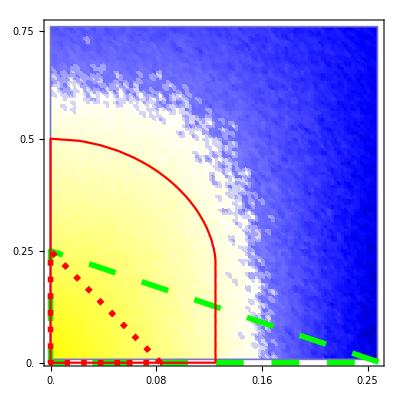

```mathematica
p0=Module[{colorfun,fs=22,ts=1.5},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],1≤ z<ts},{Lighter[Yellow,z],0<=z<1}}];Show[ListDensityPlot[Flatten[scaniPDDEP,1],ColorFunction->colorfun,ColorFunctionScaling->False,PlotRange->All,PlotRangePadding->0,
BoundaryStyle->{Black,Thickness[.003]},
FrameLabel->{{MaTeX["\\beta",FontSize->fs],None},{None,MaTeX["\\alpha",FontSize->fs]}},RotateLabel->False,
PlotLegends->BarLegend[Automatic,{0,0.5,1,1.5,2},LegendLabel->MaTeX["\\beta_{\\mathsf{DD}}/\\beta",FontSize->16],
LegendFunction->Framed,LabelStyle->Directive[16, FontFamily->"Times"]],
FrameTicks->{{{0.0,.25,0.5,{0.74,0.75}},None},{{0.0,0.08,0.16,{0.24,0.25}},None}},FrameStyle->Directive[16,FontFamily->"Times"]],RegionPlot[ConvergeBound[α,β],{α,0.0,1},{β,0.0,1},BoundaryStyle->{Green,Dashing[{0.05,0.05}],Thickness[.01]},PlotStyle->None],
RegionPlot[PDDBound1[α,β],{α,0.0,1},{β,0.0,1},BoundaryStyle->{Red,Dashing[{0.01,0.02}],Thickness[.01]},PlotStyle->None],RegionPlot[PDDBound2[α,β],{α,0.0,1},{β,0.0,1},BoundaryStyle->{Red},PlotStyle->None]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-ideal-region.pdf",p0]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/pdd-ideal-region.pdf

```mathematica
1./8
```

0.125

```mathematica
(* combning error phase *)
```

```mathematica
Module[{K,W,B0,B,A0,A},
A0=RandomHermitian[2];
A0=A0-Tr[A0]/2;
B0=RandomHermitian[2];
B0=B0-Tr[B0]/2;
{A[1],A[2],A[3],B[1],B[2],B[3]}=Table[RandomHermitian[2],6];
K=KroneckerProduct[Id,A0,Id]+0Sum[KroneckerProduct[σ[i],A[i],Id],{i,1,3}];
W=KroneckerProduct[Id,Id,B0]+0Sum[KroneckerProduct[σ[i],Id,B[i]],{i,1,3}];
{TcpNorm[MatrixLog[MatrixExp[-ⅈ K].MatrixExp[-ⅈ W]]],(TcpNorm[K]+TcpNorm[W])}
]
```

{{1.37972,0.},{5.1965,0.}}

```mathematica
data1=Transpose[Table[Module[{K,W,B0,B,A0,A,a,b},
A0=RandomHermitian[2];
A0=A0-Tr[A0]/2;
B0=RandomHermitian[2];
B0=B0-Tr[B0]/2;
{A[1],A[2],A[3],B[1],B[2],B[3]}=Table[RandomHermitian[2],6];
K=0.01*(KroneckerProduct[Id,A0]+Sum[KroneckerProduct[σ[i],A[i]],{i,1,3}]);
W=0.01*(KroneckerProduct[Id,B0]+Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}]);
{a,b}=TcpNorm[K]+TcpNorm[W];
TcpNorm[MatrixLog[MatrixExp[-ⅈ  K].MatrixExp[-ⅈ W]]]/{a(1+b),b(1+a)}
],{5000}]];
MinMax/@data1
```

{{0.0397303,0.923557},{0.26615,0.947785}}

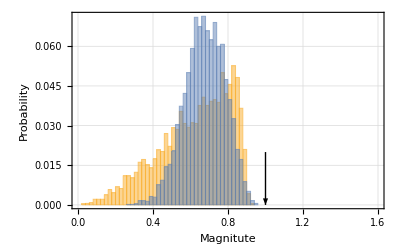

```mathematica
pbound=Histogram[data1,50,"Probability",PlotRange->{{0,1.6},All},Frame->True,FrameLabel->{"Magnitute","Probability"}, GridLines->Automatic,
ChartLegends->Placed[{MaTeX["\\widetilde\\phi_\\mathrm{B}/\\widetilde\\phi_\\mathrm{B}^{(\\mathrm{ub})}",Magnification->1.25],MaTeX["\\widetilde\\phi_\\mathrm{SB}/\\widetilde\\phi_\\mathrm{SB}^{(\\mathrm{ub})}",Magnification->1.25]},Scaled[{0.8,0.8}]],LabelStyle->12,
Epilog->{Arrow[{{1,0.02},{1,0}}]}
]
```

```mathematica
Export[NotebookDirectory[]<>"../img/approx-bound.pdf",pbound]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/notebooks/../img/approx-bound.pdf

```mathematica
(* unitray errors *)
```

```mathematica
Module[{K,W2,α,β,θ,n=2},
{α,β,θ}=RandomReal[{0.001,0.25},3];
K=KroneckerProduct[θ RandomPoint[Sphere[]].{σ[1],σ[2],σ[3]},IdentityMatrix[n]];
W2=ⅈ MatrixLog[MatrixExp[-ⅈ K].MatrixExp[-ⅈ RandomOmega[α,β,n]]];
{TcpNorm[W2],TcpNorm[W2-K]}
]
```

{{0.163257,0.165246},{0.163257,0.124372}}

```mathematica
data2=Transpose[Table[Module[{K,W2,α,β,θ,n=2},
θ=0.1;
{α,β}=RandomReal[{0.001,0.2},2];
K=KroneckerProduct[θ RandomPoint[Sphere[]].{σ[1],σ[2],σ[3]},IdentityMatrix[n]];
W2=ⅈ MatrixLog[MatrixExp[-ⅈ K].MatrixExp[-ⅈ RandomOmega[α,β,n]]];
(ErrorPhase[W2-K]/β-1)/θ^2
],{10000}]];
MinMax[data2]
```

{-0.369726,0.64918}

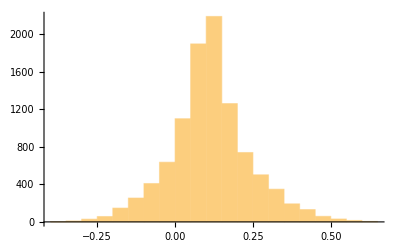

```mathematica
Histogram[data2,30,PlotRange->All]
```

```mathematica
data3=Transpose[Table[Module[{K,W,a,c,d},
{a,c,d}=RandomReal[{0.001,0.25},3];
K=RandomOmega[a,0];
W=RandomOmega[c,d];
TcpNorm[MatrixLog[MatrixExp[-ⅈ K].MatrixExp[-ⅈ W]]]/{a+c,d}
],{50000}]];
MinMax/@data3
```

{{0.0252513,0.999962},{0.991614,1.02546}}

```mathematica
Histogram[data3[[2]],100,"PDF",PlotRange->All]
```

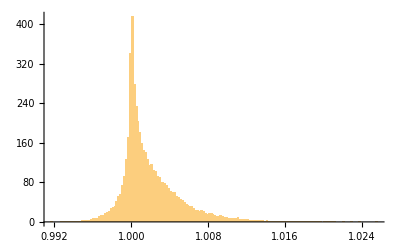

```mathematica
RandomPoint[Sphere[]].RandomBathOps[]
```

{{0.139772+0. ⅈ,-0.0709499-0.173776 ⅈ},{-0.0709499+0.173776 ⅈ,-0.500875+0. ⅈ}}

```mathematica
data4=Table[Module[{B,n=3},
{B[1],B[2],B[3]}=RandomBathOps[n];
Norm[RandomPoint[Sphere[]].{cm[B[3],B[2]],cm[B[2],B[1]],cm[B[1],B[3]]}]
],{10000}];
MinMax[data4]
```

{0.0388138,0.441991}

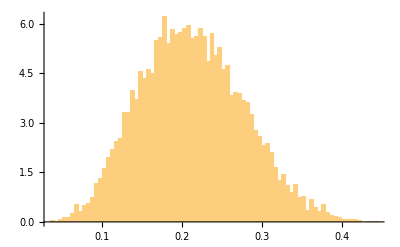

```mathematica
Histogram[data4,100,"PDF",PlotRange->All]
```

```mathematica
Module[{θ=0.1},AbsoluteTiming[
scanPDDEPn1=ParallelTable[{α,β,
1/β *Max[Table[ErrorPhase[
MatrixLog[PDD[KroneckerProduct[RandomUniRot[θ],Id].MatrixExp[-ⅈ RandomOmega[α,β]]]]
],{500}]]},{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];
]]
Export[NotebookDirectory[]<>"scanPDDEPn1.mx",scanPDDEPn1];
```

{1017.92,Null}

```mathematica
Module[{θ=0.1,amax=0.2,bmax=0.5,res=100},AbsoluteTiming[
scanPDDEPn2=ParallelTable[{α,β,
1/β *Max[Table[ErrorPhase[
MatrixLog[PDD[KroneckerProduct[RandomUniRot[θ],Id].MatrixExp[-ⅈ RandomOmega[α,β]]]]
],{1000}]]},{α,0,amax-amax/res,amax/res},{β,bmax/res,bmax,bmax/res}];
]]
Export[NotebookDirectory[]<>"scanPDDEPn2.mx",scanPDDEPn2];
```

{2273.05,Null}

```mathematica
Simplify[Maximize[{(8 α β x1)^2+(4 α β x2+4 β^2 x1 x3 )^2,x1^2+x2^2+x3^2==1&&0<α&&0<β},{x1,x2,x3}][[1]],α>0&&β>0]
```

Piecewise[{{64 α^2 β^2, α>β/(√3)}, {4 (9 α^4+10 α^2 β^2+β^4), √3 β≥3 α}, {-∞, True}}]

```mathematica
dα
```

0.0025

```mathematica
AbsoluteTiming[scanPDDEPNMax1=Module[{θ=0.1},
ParallelTable[{α,β,β^-1*Sqrt[
NMaximize[{
(8α*β*x1)^2+(4α*β*x2+4(β*x1+θ*y1)(β*x3+θ*y3))^2,x1^2+x2^2+x3^2==1&&y1^2+y3^3==1},
{x1,x2,x3,y1,y3}][[1]]]},
{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}]];]
```

{981.591,Null}

```mathematica
{αmax,βmax,dα,dβ}
```

{0.25,0.75,0.0025,0.0075}

```mathematica
0.3/50
```

0.006

```mathematica
AbsoluteTiming[scanPDDEPNMax1r=Module[{θ=0.1},
Table[{α,β,
NMaximize[{
(8α*x1)^2+(4α*x2+4(x1+θ/β*y1)(β x3+θ*y3))^2,x1^2+x2^2+x3^2==1&&y1^2+y3^3==1},
{x1,x2,x3,y1,y3},Method->"RandomSearch",AccuracyGoal->4
][[1]]
},
{α,0,0.1,0.0025},{β,dβ,0.3,0.075}]];]
```

```mathematica
AbsoluteTiming[scanPDDEPNMax1r=Module[{θ=0.1},
ParallelTable[{α,β,
NMaximize[{
(8α*x1)^2+(4α*x2+4(x1+θ/β*y1)(β x3+θ*y3))^2,x1^2+x2^2+x3^2==1&&y1^2+y3^3==1},
{x1,x2,x3,y1,y3},Method->"RandomSearch",AccuracyGoal->6
][[1]]
},
{α,0,0.1,0.002},{β,dβ,0.3,0.006}]];]
```

{2646.74,Null}

```mathematica
Sqrt[#[[3]]]&\@Flatten[scanPDDEPNMax1r,1]
```

```mathematica
Export[NotebookDirectory[]<>"scanPDDEPNMax1r.mx",scanPDDEPNMax1r];
```

```mathematica
AbsoluteTiming[scanPDDEPNMaxa1=Module[{θ=0.1},
ParallelTable[{α,β,(4/β)*Sqrt[
NMaximize[{(2α*β*x1)^2+(α*β*x2+β^2 x1 x3+θ β √(x1^2+x3^2)+θ^2/2)^2,
x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]]]},
{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}]];]
```

{402.991,Null}

```mathematica
AbsoluteTiming[scanPDDEPNMaxb1=Module[{θ=0.1},
ParallelTable[{α,β,(4/β)*Sqrt[
NMaximize[{(2α*β*x1)^2+(α*β*x2+β^2 x1 x3+θ β √(x1^2+x3^2)+θ^2/2)^2,
x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]]]},
{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}]];]
```

```mathematica
Export[NotebookDirectory[]<>"scanPDDEPNMax1.mx",scanPDDEPNMax1];
```

```mathematica
PDDBound1
```

```mathematica
PDDBounderr[a_,b_,θ_]:=(a+(θ b^2)/3>(b+θ)/(√3)&&0<a+(θ b^2)/3<b/(8 b+8 θ))||(a+(θ b^2)/3≤ (b+θ)/(√3)&&(9 (a+(θ b^2)/3)^4+10 (a+(θ b^2)/3)^2(b+θ)^2+(b+θ)^4)/(b+θ)^2<b^2/(4(b+θ)^2))
PDDBounderr2[a_,b_,θ_]:=(a>(b+θ)/(√3)&&0<a<b/(8 b+8 θ))||(a≤ (b+θ)/(√3)&&(9 (a)^4+10 (a)^2(b+θ)^2+(b+θ)^4)/(b+θ)^2<b^2/(4(b+θ)^2))
PDDBounderr3[a_,b_,θ_]:=(an>nb/(√3)&&0<an<b/(8 nb))||(an≤ nb/(√3)&&(9 (an)^4+10 (an)^2(nb)^2+(nb)^4)/(nb)^2<b^2/(4(nb)^2))/.{an->a+b^2θ/3,nb->(β+θ)}
```

```mathematica
{#[[1]],#[[2]],Sqrt[#[[3]]]}&/@Flatten[scanPDDEPNMax1r,1]
```

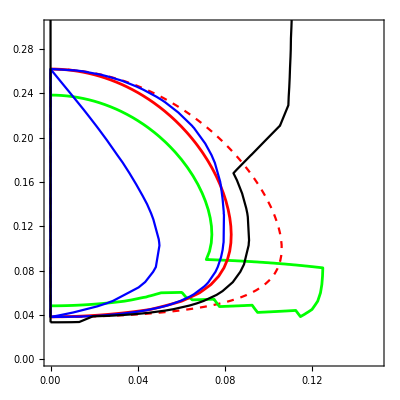

```mathematica
Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
Show[
RegionPlot[2α^2+(θ+β)^4/(4β^2)≤1/16,{α,0.0,0.15},{β,0.0,0.3},BoundaryStyle->{Red,Dashed},PlotStyle->None],
ListContourPlot[Flatten[scanPDDEPNMax1,1],ContourShading->None,Contours->{1},ContourStyle->Directive[Green,Opacity[1],Thickness[.005]]],
ListContourPlot[Flatten[scanPDDEPNMaxa1,1],ContourShading->None,Contours->{1},ContourStyle->Directive[Red,Opacity[1],Thickness[.005]]],
RegionPlot[(4α^2+(θ+β)^4/(3β^2)≤ 1/16&&3α>(θ+β)^2/(2β))||(α+(θ+β)^2/(2β)≤ 1/4&&3α≤(θ+β)^2/(2β)),{α,0.0,1},{β,0.0,1},BoundaryStyle->Blue,PlotStyle->None],
RegionPlot[{(4 α^2+(θ (2 β+θ) (2 β^2+2 β θ+θ^2))/(4 β^2)≤1/16&&2 α>β)||((16 α^4+8 α^2 β^2+(β+θ)^4)/(4 β^2)≤ 1/16)},{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Blue],
RegionPlot[regapprox[α,β,θ],{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Black]
]]
```

```mathematica
Module[{θ=0.},
Show[
RegionPlot[regapprox[α,β,θ],{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Black],
RegionPlot[{(4 α^2<1/16&&√3 β≤3 α)||((9 α^4+10 α^2 β^2+β^4)/(4 β^2)<1/16&&√3 β>3 α)},{α,0,0.25},{β,0,0.5},PlotStyle->None,BoundaryStyle->Black],
RegionPlot[{(4 α^2<1/16&&2 α>β)||(((4 α^2+β^2)^2)/(4 β^2)<1/16&&2 α≤β)},{α,0,0.25},{β,0,0.5},PlotStyle->None],RegionPlot[rootfun[α,β,θ] <1/16||β/2<α<1/8,{α,0,1},{β,0,1}]
]
]
```

$Aborted

```mathematica
Simplify[Maximize[{(2 α x1)^2+(α x2 +β x1 x3)^2,x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]],α>0&&β>0]
```

Piecewise[{{4 α^2, α≥Root[-β^4-6 β^2 #1^2+3 #1^4&,2]||√3 β≤3 α||α≤Root[-β^4-6 β^2 #1^2+3 #1^4&,1]}, {(9 α^4+10 α^2 β^2+β^4)/(4 β^2), √3 β>3 α}, {0, True}}]

```mathematica
Solve[2α^2 +(θ+β)^4/(4β^2)==1/16,θ]
```

{{θ→-β-(√(-√(4 β^4-β^2 (-1+32 α^2+4 β^2))))/(√2)},{θ→-β+(√(-√(4 β^4-β^2 (-1+32 α^2+4 β^2))))/(√2)},{θ→-β-((4 β^4-β^2 (-1+32 α^2+4 β^2))^(1/4))/(√2)},{θ→-β+((4 β^4-β^2 (-1+32 α^2+4 β^2))^(1/4))/(√2)}}

```mathematica
Simplify[Normal[Series[-β+((4 β^4-β^2 (-1+32 α^2+4 β^2))^(1/4))/(√2),{α,0,2},{β,0,1}]],β>0]
```

((1-8 α^2) √β)/(√2)-β

```mathematica
(2^n α x1)^2+(θr+β x1 x3)^2/.{n->1,x1->t,x3->√(1-t^2)}
```

4 t^2 α^2+(t √(1-t^2) β+θr)^2

```mathematica
Expand[4 t^2 α^2+(t √(1-t^2) β+θr)^2]
```

4 t^2 α^2+t^2 β^2-t^4 β^2+2 t √(1-t^2) β θr+θr^2

```mathematica
Maximize[4 t^2 α^2+t^2 β^2-t^4 β^2+ β θr+θr^2,t][[1]]
```

Piecewise[{{θr^2, β==0&&α==0}, {(16 α^4+8 α^2 β^2+β^4+4 β^3 θr+4 β^2 θr^2)/(4 β^2), β>0||β<0}, {∞, True}}]

```mathematica
Simplify[Maximize[{4 t^2 α^2+(t √(1-t^2) β+θr)^2,0<t<1&&α>0&&β>0&&θr≥0},t][[1]],α>0&&β>0&&θr≥ 0]
```

Piecewise[{{4 α^2, 2 α>β&&θr==0}, {-Root[(1024 α^10+1024 α^8 β^2+384 α^6 β^4+64 α^4 β^6+4 α^2 β^8) #1+(256 α^8+768 α^6 β^2+352 α^4 β^4+48 α^2 β^6+β^8) #1^2+(128 α^4 β^2+128 α^2 β^4+8 β^6) #1^3+16 β^4 #1^4&,1], θr==0&&2 α≤β}, {-Root[1024 α^10 θr^2+768 α^8 β^2 θr^2+192 α^6 β^4 θr^2+16 α^4 β^6 θr^2+256 α^8 θr^4+1280 α^6 β^2 θr^4-128 α^4 β^4 θr^4+256 α^4 β^2 θr^6+(1024 α^10+1024 α^8 β^2+384 α^6 β^4+64 α^4 β^6+4 α^2 β^8+512 α^8 θr^2+2048 α^6 β^2 θr^2+352 α^4 β^4 θr^2-32 α^2 β^6 θr^2+640 α^4 β^2 θr^4+64 α^2 β^4 θr^4) #1+(256 α^8+768 α^6 β^2+352 α^4 β^4+48 α^2 β^6+β^8+512 α^4 β^2 θr^2+192 α^2 β^4 θr^2-8 β^6 θr^2+16 β^4 θr^4) #1^2+(128 α^4 β^2+128 α^2 β^4+8 β^6+32 β^4 θr^2) #1^3+16 β^4 #1^4&,1], True}}]

```mathematica
Simplify[Maximize[{t √(1-t^2) β+θr,0<t<1},t][[1]]/.θr->θ^2/(2β)+θ,β>0]==1/4
```

(β+θ)^2/(2 β)==1/4

```mathematica
Solve[(β+θ)^2/(2 β)==1/4,{θ},Reals]
```

{{θ→ConditionalExpression[-(√β)/(√2)-β, β>0]},{θ→ConditionalExpression[(√β)/(√2)-β, β>0]}}

```mathematica
Maximize[(√β)/(√2)-β,β]
```

{1/8,{β→1/8}}

```mathematica
1/32.
```

0.03125

```mathematica
Simplify[Maximize[{t^2 α^2+(t √(1-t^2) β)^2,0<t<1&&α>0&&β>0},t][[1]],α>0&&β>0]
```

Piecewise[{{α^2, α>β}, {((α^2+β^2)^2)/(4 β^2), α≤β}, {-∞, True}}]

```mathematica
rootfun[α_,β_,θ_]:=Module[{θr=θ^2/(2β)+θ},
-Root[1024 α^10 θr^2+768 α^8 β^2 θr^2+192 α^6 β^4 θr^2+16 α^4 β^6 θr^2+256 α^8 θr^4+1280 α^6 β^2 θr^4-128 α^4 β^4 θr^4+256 α^4 β^2 θr^6+(1024 α^10+1024 α^8 β^2+384 α^6 β^4+64 α^4 β^6+4 α^2 β^8+512 α^8 θr^2+2048 α^6 β^2 θr^2+352 α^4 β^4 θr^2-32 α^2 β^6 θr^2+640 α^4 β^2 θr^4+64 α^2 β^4 θr^4) #1+(256 α^8+768 α^6 β^2+352 α^4 β^4+48 α^2 β^6+β^8+512 α^4 β^2 θr^2+192 α^2 β^4 θr^2-8 β^6 θr^2+16 β^4 θr^4) #1^2+(128 α^4 β^2+128 α^2 β^4+8 β^6+32 β^4 θr^2) #1^3+16 β^4 #1^4&,1]]
```

```mathematica
{αmax,βmax}={0.25,0.5};
{dα,dβ}={αmax,βmax}/100;
```

```mathematica
θfun[α_,β_]:=Module[{θ},If[!(((4 α^2+β^2)^2)/(4 β^2)≤ 1/16||β/2<α<1/8),0,
θ/.FindRoot[rootfun[α,β,θ]==1/16,{θ,0.1}]]]
```

```mathematica
AbsoluteTiming[θlist=ParallelTable[{α,β,θfun[α,β]},{α,0,αmax,dα},{β,dβ,βmax,dβ}];]
```

Parallel`Protected`PacketHandler::default: Unhandled packet OutputNamePacket[Out[1]= ] received and discarded from ….

Parallel`Protected`PacketHandler::default: Unhandled packet ReturnExpressionPacket[BoxData[$Aborted,StandardForm]] received and discarded from ….

Parallel`Protected`PacketHandler::default: Unhandled packet InputNamePacket[In[2]:= ] received and discarded from ….

General::stop: Further output of Parallel`Protected`PacketHandler::default will be suppressed during this calculation.

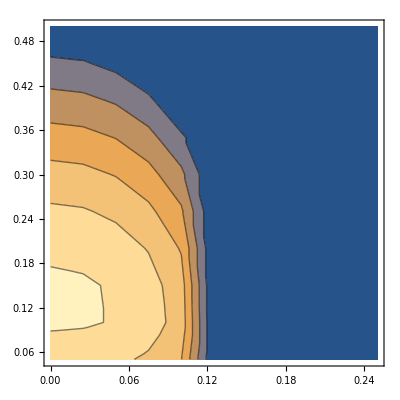

```mathematica
ListContourPlot[Flatten[θlist,1]]
```

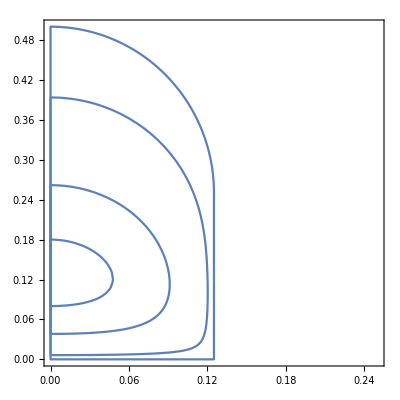

```mathematica
Show[
RegionPlot[{((4 α^2+β^2)^2)/(4 β^2)≤1/16||β/2<α<1/8},{α,0,0.25},{β,0,0.5},PlotStyle->None],
RegionPlot[rootfun[α,β,0.01]== 1/16,{α,0,0.25},{β,0,0.5}],
RegionPlot[rootfun[α,β,0.05]≤ 1/16,{α,0,0.25},{β,0,0.5},PlotStyle->None],
RegionPlot[rootfun[α,β,0.1]≤ 1/16,{α,0,0.25},{β,0,0.5},PlotStyle->None],
RegionPlot[rootfun[α,β,0.12]≤ 1/16,{α,0,0.25},{β,0,0.5},PlotStyle->None]
]
```

```mathematica
ContourPlot[]
```

```mathematica
4 α^2+θr^2/.θr->(θ^2/(2β)+θ)
```

4 α^2+(θ+θ^2/(2 β))^2

```mathematica
rootfun[α_,β_,θ_]:=Maximize[{2^2 t^2 α^2+(t √(1-t^2) β+θ^2/(2β)+θ)^2,0<t<1},t][[1]]
```

```mathematica
Expand[(2 α x1)^2+(θr+β x1 x3)^2]
```

4 x1^2 α^2+x1^2 x3^2 β^2+2 x1 x3 β θr+θr^2

```mathematica
FullSimplify[Maximize[{4 x1^2 α^2+x1^2 x3^2 β^2+ β (θ^2/(2β)+θ)+ (θ^2/(2β)+θ)^2,x1^2+x3^2==1},{x1,x3}][[1]],α>0&&β>0]
```

Piecewise[{{4 α^2+(θ (2 β+θ) (2 β^2+2 β θ+θ^2))/(4 β^2), 2 α>β}, {(16 α^4+8 α^2 β^2+(β+θ)^4)/(4 β^2), True}}]

```mathematica
FullSimplify[Maximize[{4 x1^2 α^2+1/4  β^2+ 2x1 x3 β (θ^2/(2β)+θ)+ (θ^2/(2β)+θ)^2,x1^2+x3^2==1},{x1,x3}][[1]],α>0&&β>0]
```

Piecewise[{{4 α^2+β^2/4, θ==0}, {(8 α^2 β^2+β^4+4 β θ^3+θ^4+2 β^2 (2 θ^2+√(16 α^4+θ^2 (2 β+θ)^2)))/(4 β^2), True}}]

```mathematica
Module[{α=0.0
((2 x1)^2+(η+x2+x1 x3)^2,x1^2+x2^2+x3^2==1
```

```mathematica
NSolve[{Maximize[{(2 x1)^2+(η+x2+x1 x3)^2,x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]]==5,η>0},η]
```

{{η→0.738017}}

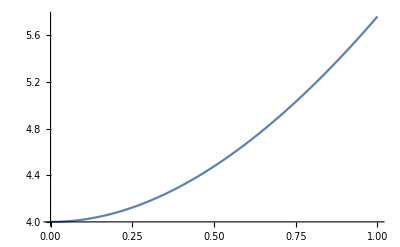

```mathematica
Plot[-Root[-400-272 η^2-32 η^4+16 η^6+(-160+24 η^2+40 η^4) #1+(9+30 η^2+η^4) #1^2+(10+2 η^2) #1^3+#1^4&,1],{η,0,1}]
```

```mathematica
Simplify[(9 (an)^4+10 (an)^2(nb)^2+(nb)^4)/(nb)^2==β^2/(4(nb)^2)/.{an->α,nb->(β+θ)}]
```

10 α^2+(9 α^4)/(β+θ)^2+(β+θ)^2==β^2/(4 (β+θ)^2)

```mathematica
Normal[Series[10 α^2+(9 α^4)/(β+θ)^2+(β+θ)^2-β^2/(4 (β+θ)^2),{α,0,2},{β,0,2},{θ,0,2}]]
```

10 α^2+β^2 (1-1/(4 θ^2))+2 β θ+θ^2

```mathematica
10 α^2+(β+θ)^2==(β/(2θ))^2
```

10 α^2+(β+θ)^2==β^2/(4 θ^2)

```mathematica
U={{1,-θ3,θ2},{θ3,1,-θ1},{-θ2,θ1,1}}
```

{{1,-θ3,θ2},{θ3,1,-θ1},{-θ2,θ1,1}}

```mathematica
U.Uᵀ
```

{{1+θ2^2+θ3^2,-θ1 θ2,-θ1 θ3},{-θ1 θ2,1+θ1^2+θ3^2,-θ2 θ3},{-θ1 θ3,-θ2 θ3,1+θ1^2+θ2^2}}

```mathematica
Simplify[Norm[{{1,-θ3,θ2},{θ3,1,-θ1},{-θ2,θ1,1}}],θ1^2+θ2^2+θ3^2==1&&{θ1,θ2,θ3}∈Reals]
```

Max[√Root[-1-2 θ1^2-θ1^4-2 θ2^2-2 θ1^2 θ2^2-θ2^4-2 θ3^2-2 θ1^2 θ3^2-2 θ2^2 θ3^2-θ3^4+(3+4 θ1^2+θ1^4+4 θ2^2+2 θ1^2 θ2^2+θ2^4+4 θ3^2+2 θ1^2 θ3^2+2 θ2^2 θ3^2+θ3^4) #1+(-3-2 θ1^2-2 θ2^2-2 θ3^2) #1^2+#1^3&,1],√Root[-1-2 θ1^2-θ1^4-2 θ2^2-2 θ1^2 θ2^2-θ2^4-2 θ3^2-2 θ1^2 θ3^2-2 θ2^2 θ3^2-θ3^4+(3+4 θ1^2+θ1^4+4 θ2^2+2 θ1^2 θ2^2+θ2^4+4 θ3^2+2 θ1^2 θ3^2+2 θ2^2 θ3^2+θ3^4) #1+(-3-2 θ1^2-2 θ2^2-2 θ3^2) #1^2+#1^3&,2],√Root[-1-2 θ1^2-θ1^4-2 θ2^2-2 θ1^2 θ2^2-θ2^4-2 θ3^2-2 θ1^2 θ3^2-2 θ2^2 θ3^2-θ3^4+(3+4 θ1^2+θ1^4+4 θ2^2+2 θ1^2 θ2^2+θ2^4+4 θ3^2+2 θ1^2 θ3^2+2 θ2^2 θ3^2+θ3^4) #1+(-3-2 θ1^2-2 θ2^2-2 θ3^2) #1^2+#1^3&,3]]

```mathematica
Sqrt[x/.Solve[10 α^2+x==β^2/(4 x),x][[2]]]
```

(√(-10 α^2+√(100 α^4+β^2)))/(√2)

```mathematica
Simplify[Normal[Series[(√(-10 α^2+√(100 α^4+β^2)))/(√2),{α,0,2},{β,0,2}]],α>0&&β>0]
```

(-5 α^2+β)/(√2 √β)

1-x/2+x^2/12+O[x]^4

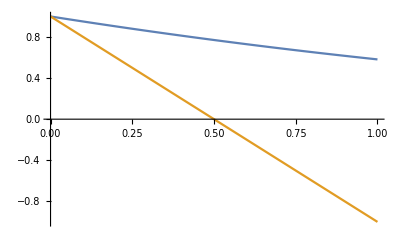

```mathematica
Plot[{-x/(1-E^x),1-2x},{x,0,1}]
```

```mathematica
Normal[Series[(β+θ)^2+10 (α+(β^2 θ)/3)^2+(9 (α+(β^2 θ)/3)^4)/(β+θ)^2,{α,0,2},{β,0,2},{θ,0,2}]]
```

10 α^2+β^2+2 β θ+20/3 α β^2 θ+θ^2

```mathematica
Normal[Series[(β+θ)^2+10 (α+(β^2 θ)/3)^2+(9 (α+(β^2 θ)/3)^4)/(β+θ)^2,{α,0,2},{β,0,2},{θ,0,2}]]
```

10 α^2+β^2+2 β θ+20/3 α β^2 θ+θ^2

```mathematica
Normal[Series[β^2/(4 (β+θ)^2),{β,0,2},{θ,0,2}]]
```

β^2/(4 θ^2)

```mathematica
Simplify[a≤ √(1/4^(n+2))]
```

4 a≤√(4^-n)

```mathematica
Solve[(θ+β)^4/(4 β^2)==1/16,θ]
```

{{θ→1/2 (-√2 √-β-2 β)},{θ→1/2 (√2 √-β-2 β)},{θ→1/2 (-√2 √β-2 β)},{θ→1/2 (√2 √β-2 β)}}

```mathematica
Maximize[1/2 (√2 √β-2 β),β]
```

{1/8,{β→1/8}}

```mathematica
Solve[10 α^2+x==β^2/(4x),{x},Reals]
```

{{x→-5 α^2-1/2 √(100 α^4+β^2)},{x→-5 α^2+1/2 √(100 α^4+β^2)}}

```mathematica
Simplify[Series[√(β/2+(5 α^2)^2)-5 α^2,{α,0,2},{β,0,2}],α>0]
```

((√β)/(√2)+O[β]^(5/2))-5 α^2+O[α]^3

```mathematica
Simplify[Normal[Series[(10 β^4 θ^2)/9+(β^8 θ^4)/(9 (β+θ)^2)+(β+θ)^2,{β,0,2},{θ,0,2}]]≤β^2/(4 (β+θ)^2),β>0&&θ>0]
```

(β+θ)^2≤β^2/(4 (β+θ)^2)

```mathematica
(β+θ)^2≤β/2
```

(β+θ)^2≤β/2

```mathematica
10α^2+(β+θ)^2≤β^2/(4 (β+θ)^2)
```

```mathematica
Reduce[10α^2+(β+θ)^2≤β^2/(4 (β+θ)^2)&&α>0&&β>0&&θ>0,{θ},Reals]
```

0<α<1/(2 √10)&&0<β<1/2 √(1-40 α^2)&&0<θ≤Root[-β^2+40 α^2 β^2+4 β^4+(80 α^2 β+16 β^3) #1+(40 α^2+24 β^2) #1^2+16 β #1^3+4 #1^4&,2]

```mathematica
p3=Module[{colorfun,fs=15,ts=22,t0=1},
colorfun[x_]:=ColorData["Rainbow"][x];
Show[
RegionPlot[regapprox[α,β,0.01],{α,0.0,0.2},{β,0.0,0.5},
BoundaryStyle->{colorfun[0.2],Thickness[.002]},PlotStyle->Lighter[colorfun[0.2],0.8],
FrameLabel->{{MaTeX["\\beta",FontSize->ts],None},{None,MaTeX["\\alpha",FontSize->ts]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
PlotRangePadding->0,
Epilog->{
Text[Framed[Style["0.",fs,FontFamily->"Times"],Background->Lighter[colorfun[0.2],0.8],FrameStyle->Gray],{0.125,0.13}],
Text[Framed[Style["0.04",fs,FontFamily->"Times"],Background->Lighter[colorfun[0.4],0.8],FrameStyle->Gray],{0.095,0.13}],
Text[Framed[Style["0.08",fs,FontFamily->"Times"],Background->Lighter[colorfun[0.6],0.8],FrameStyle->Gray],{0.065,0.13}],
Text[Framed[Style["0.12",fs,FontFamily->"Times"],Background->Lighter[colorfun[0.8],0.8],FrameStyle->Gray],{0.02,0.13}]
}
],
RegionPlot[regapprox[α,β,0.04],{α,0.0,1},{β,0.0,1},BoundaryStyle->{colorfun[2/5],,Thickness[.003]},PlotStyle->Lighter[colorfun[0.4],0.8]],
RegionPlot[regapprox[α,β,0.08],{α,0.0,1},{β,0.0,1},BoundaryStyle->{colorfun[3/5],,Thickness[.003]},PlotStyle->Lighter[colorfun[0.6],0.8]],
RegionPlot[regapprox[α,β,0.12],{α,0.0,1},{β,0.0,1},BoundaryStyle->{colorfun[4/5],,Thickness[.003]},PlotStyle->Lighter[colorfun[0.8],0.8]]
]]
```

$Aborted

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-noisy-region.pdf",p3]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/pdd-noisy-region.pdf

```mathematica
Maximize[{(2α x1)^2+(α x2+β x1 x3+θr )^2,x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]]
```

$Aborted

```mathematica
AbsoluteTiming[scanPDDEPNMax1β=Module[{θ=0.1,α=0.08},
ParallelTable[{β,4*Sqrt[
NMaximize[{4(α*x1)^2+(α*x2+β^-1(β*x1+θ*y1)(β*x3+θ*y3))^2,
x1^2+x2^2+x3^2==1&&y1^2+y3^3==1},{x1,x2,x3,y1,y3}][[1]]]},{β,0.01,0.25,0.01}]];]
```

{2.90441,Null}

```mathematica
AbsoluteTiming[scanPDDEPNMax1β2=Module[{θ=0.1,α=0.08},
Table[{β,4*Sqrt[
NMaximize[{4(α*x1)^2+(α*x2+β^-1(β*x1+θ*y1)(β*x3+θ*y3))^2,
x1^2+x2^2+x3^2==1&&y1^2+y3^3==1},{x1,x2,x3,y1,y3},Method->"RandomSearch"][[1]]]},{β,0.03,0.1,0.003}]];]
```

{48.3962,Null}

```mathematica
AbsoluteTiming[scanPDDEPNMax1β3=Module[{θ=0.1,α=0.08},
Table[{β,(4/β)*Sqrt[
NMaximize[{4(α*β*x1)^2+(α*β*x2+β^2 x1 x3+θ β x2+θ^2/2)^2,
x1^2+x2^2+x3^2==1},{x1,x2,x3}][[1]]]},{β,0.03,0.1,0.003}]];]
```

{3.24184,Null}

```mathematica
Maximize[{4α^2 x1^2+β^2 (x1+λ y1)^2(x3+λ y3)^2,x1^2+x3^2==1&&y1^2+y3^2==1&&0<α&&0<β&&0<λ},{x1,x3,y1,y3}][[1]]
```

$Aborted

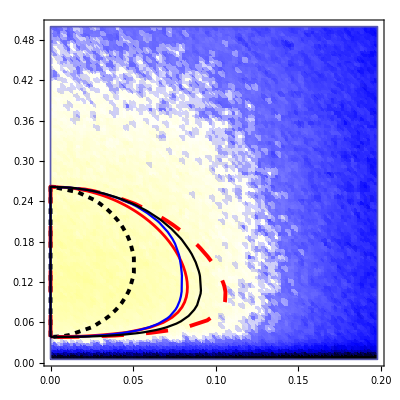

```mathematica
p1=Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];Show[ListDensityPlot[Flatten[scanPDDEPn2,1],ColorFunction->colorfun,ColorFunctionScaling->False,PlotRange->All,PlotRangePadding->0,
BoundaryStyle->{Black,Thickness[.003]},
Epilog->Text[MaTeX["\\theta=0.1",FontSize->fs],Scaled[{0.9,0.95}],Background->White],
FrameLabel->{{MaTeX["\\beta",FontSize->fs],None},{None,MaTeX["\\alpha",FontSize->fs]}},RotateLabel->False,
PlotLegends->BarLegend[Automatic,{0,0.5,0.8,1,1.2,2},LegendLabel->MaTeX["\\beta_{\\mathsf{DD}}/\\beta",FontSize->16],
LegendFunction->Framed,LabelStyle->Directive[16, FontFamily->"Times"]],
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"]],
ListContourPlot[Flatten[scanPDDEPNMaxa1,1],ContourShading->None,Contours->{1},ContourStyle->Directive[Red,Opacity[1],Thickness[.005]]],
RegionPlot[PDDBounderr3[α,β,0.1],{α,0.0,1},{β,0.0,1},BoundaryStyle->{Black,Dashing[{0.01,0.01}],Thickness[.007]},PlotStyle->None],
RegionPlot[2 α^2+(0.1+β)^4/(4 β^2)≤1/16,{α,0.0,1},{β,0.0,1},BoundaryStyle->{Red,Dashing[{0.04,0.04}],Thickness[.007]},PlotStyle->None],
RegionPlot[{(4 α^2+(θ (2 β+θ) (2 β^2+2 β θ+θ^2))/(4 β^2)≤1/16&&2 α>β)||((16 α^4+8 α^2 β^2+(β+θ)^4)/(4 β^2)≤ 1/16)},{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Blue],
RegionPlot[regapprox[α,β,θ]≤1/16,{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Black]
,ImageSize->400]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/npdd-region-num.pdf",p1]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/npdd-region-num.pdf

```mathematica
AbsoluteTiming[NPDDEP02sc=ParallelTable[
{α,β,Max[Table[
Module[{Ω,Γ,θ=0.05},
Ω=RandomOmega[α,β];
Γ=θ Normalize[RandomVariate[NormalDistribution[],3]].{σ[1],σ[2],σ[3]};
ErrorPhase[PDDMap[KroneckerProduct[MatrixExp[-ⅈ Γ],Id].MatrixExp[-ⅈ Ω]]]],{1000}]]/β}
,{α,0.0025,0.25,0.0025},{β,0.005,0.5,0.005}
];]
```

{2176.34,Null}

```mathematica
Export[NotebookDirectory[]<>"NPDDEP02sc.mx",NPDDEP02sc];
```

```mathematica
Maximize[{4a^2 x1^2+(a x2+b x1 x3)^2,x1^2+x2^2+x3^2==1&&b>0&&a>0},{x1,x2,x3}][[1]]
```

Piecewise[{{4 a^2, b>0&&a>(√(b^2))/(√3)}, {(9 a^4+10 a^2 b^2+b^4)/(4 b^2), (b>0&&a==(√(b^2))/(√3))||(b>0&&0<a<(√(b^2))/(√3))}, {-∞, True}}]

```mathematica
Reduce[4 a^2<b^2/(16(b+θ)^2)&&a>0&&b>0&&θ>0]
```

b>0&&θ>0&&0<a<b/(8 b+8 θ)

```mathematica
Reduce[(9 a^4+10 a^2 b^2+b^4)/b^2<b^2/(4(b+θ)^2)&&a>0&&b>0&&θ>0]
```

0<b<1/2&&0<θ<1/2 (1-2 b)&&0<a<Root[-b^4+4 b^6+8 b^5 θ+4 b^4 θ^2+(40 b^4+80 b^3 θ+40 b^2 θ^2) #1^2+(36 b^2+72 b θ+36 θ^2) #1^4&,2]

```mathematica
Module[{θ=0.1},
AbsoluteTiming[ParallelTable[
ErrorPhase[MatrixLog[
PDDn[ MatrixExp[-ⅈ RandomOmega[α,β]] ,Z.RandomUniRot[θ],X.RandomUniRot[θ]]
]]/β,{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
]
```

{3.89572,Null}

```mathematica
Module[{θ=0.1},
AbsoluteTiming[scanPDDru01=Table[{α,β,
Max[ParallelTable[ErrorPhase[
MatrixLog[PDDn[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.RandomUniRot[θ],X.RandomUniRot[θ]]]],{100}]]/β
},{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
]
```

{594.581,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDru01.mx",scanPDDru01];
```

```mathematica
Needs["MaTeX`"]
```

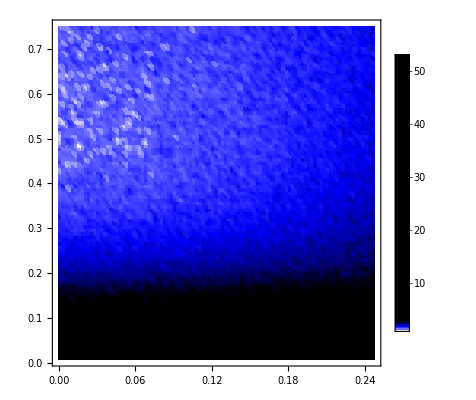

```mathematica
p3=Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
ListDensityPlot[
Flatten[scanPDDru01,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\theta=0.1",FontSize->fs],Scaled[{0.9,0.95}],Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\beta",FontSize->fs],None},{None,MaTeX["\\alpha",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400]]
```

```mathematica
Module[{θ=0.1},
AbsoluteTiming[scanPDDru01c=Table[{α,β,
Max[ParallelTable[
U = RandomUniRot[θ];
ErrorPhase[
MatrixLog[PDDn[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.U,X.U]]],{100}]]/β
},{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
]
```

{602.405,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDru01c.mx",scanPDDru01c];
```

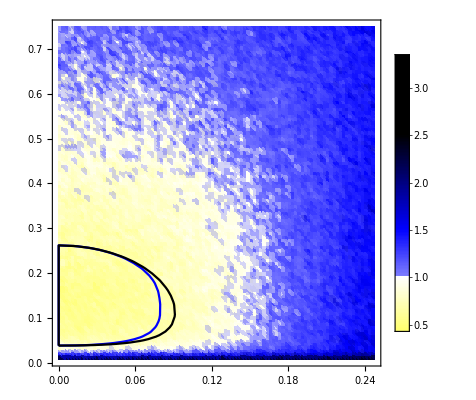

```mathematica
p3=Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
Show[ListDensityPlot[
Flatten[scanPDDru01c,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\theta=0.1",FontSize->fs],Scaled[{0.9,0.95}],Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\beta",FontSize->fs],None},{None,MaTeX["\\alpha",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
RegionPlot[{(4 α^2+(θ (2 β+θ) (2 β^2+2 β θ+θ^2))/(4 β^2)≤1/16&&2 α>β)||((16 α^4+8 α^2 β^2+(β+θ)^4)/(4 β^2)≤ 1/16)},{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Blue],
RegionPlot[rootfun[α,β,θ]≤1/16,{α,0,0.5},{β,0,1},PlotStyle->None,BoundaryStyle->Black]
]]
```

```mathematica
Module[{θ=0.01,αmax=0.25,βmax=0.5,dα,dβ},
{dα,dβ}={αmax,βmax}/100;
AbsoluteTiming[scanPDDru001=ParallelTable[{α,β,
Max[Table[ErrorPhase[
MatrixLog[PDDn[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.RandomUniRot[θ],X.RandomUniRot[θ]]]],{100}]]/β
},{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
]
```

```mathematica
Export[NotebookDirectory[]<>"scanPDDru001.mx",scanPDDru001];
```

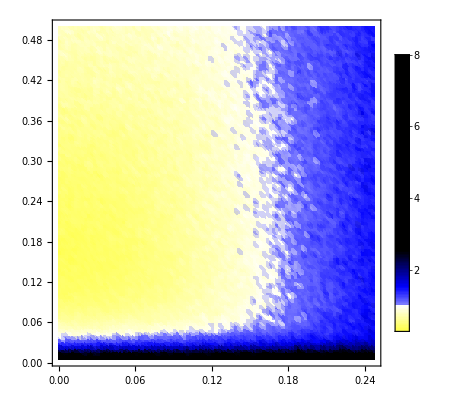

```mathematica
Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
ListDensityPlot[
Flatten[scanPDDru001,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\theta=0.01",FontSize->fs],Scaled[{0.9,0.95}],Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\beta",FontSize->fs],None},{None,MaTeX["\\alpha",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400]]
```

```mathematica
-MatrixExp[-ⅈ (π/2)Z].MatrixExp[-ⅈ (π/2)X].MatrixExp[-ⅈ (π/2)Z].MatrixExp[-ⅈ (π/2)X]
```

{{1,0},{0,1}}

```mathematica
RandomOmega[0,1]
```

1.

```mathematica
Module[{α=0.03,βmax=0.1,ηmax=0.06,nres=100,dβ,dη,Zn,Xn,Un},
dη=ηmax/nres;
dβ=βmax/nres;
AbsoluteTiming[scanPDDnpulse003=ParallelTable[{β,η,
Max[Table[
Un=MatrixExp[-ⅈ*RandomOmega[α,β]];
Zn=MatrixExp[-ⅈ (π/2KroneckerProduct[Z,Id]+η RandomOmega[0,1])];
Xn=MatrixExp[-ⅈ (π/2KroneckerProduct[X,Id]+η RandomOmega[0,1])];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{300}]]/β
},{β,dβ,βmax,dβ},{η,0,ηmax-dη,dη}];]
]
```

{1241.08,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDnpulse003.mx",scanPDDnpulse003];
```

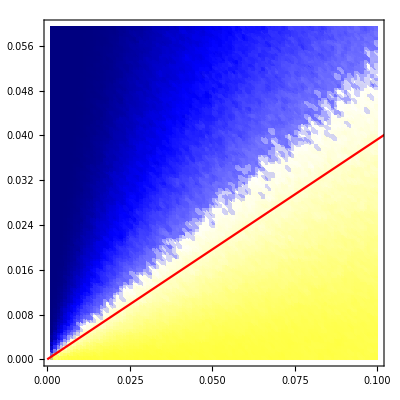

```mathematica
picPDDnpulse=Module[{colorfun,fs=22},
colorfun[x_]:=Module[{z=2-2^(1-x),ts=1.5,t0=1.},Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}]];
Show[
ListDensityPlot[
Flatten[scanPDDnpulse003,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
FrameLabel->{{MaTeX["\\eta",FontSize->fs],None},{None,MaTeX["\\phi_\\mathrm{SB}",FontSize->fs]}},RotateLabel->False,
PlotLegends->BarLegend[{colorfun,{0,10}},{0,0.5,1,1.5,2,3,4},LegendMarkerSize->300,
LegendLabel->MaTeX["\\Phi_{\\mathrm{SB}}/\\phi_{\\mathrm{SB}}",FontSize->16],LabelStyle->Directive[15,FontFamily->"Times"]],
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[{π/8x},{x,0,1},PlotStyle->Red]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-noisypulse.pdf",picPDDnpulse]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/mathematica/../img/pdd-noisypulse.pdf

```mathematica
Module[{α=0.1,βmax=0.75,ηmax=0.5,nres=100,dβ,dη,Zn,Xn,Un},
dη=ηmax/nres;
dβ=βmax/nres;
AbsoluteTiming[scanPDDnpulseα01=ParallelTable[{β,η,
Max[Table[
Un=MatrixExp[-ⅈ*RandomOmega[α,β]];
Zn=MatrixExp[-ⅈ (π/2KroneckerProduct[Z,Id]+η RandomOmega[0,1])];
Xn=MatrixExp[-ⅈ (π/2KroneckerProduct[X,Id]+η RandomOmega[0,1])];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{300}]]/β
},{β,dβ,βmax,dβ},{η,0,ηmax-dη,dη}];]
]
```

{1679.97,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDnpulseα01.mx",scanPDDnpulseα01];
```

```mathematica
Module[{α=0.05,βmax=0.75,ηmax=0.4,nres=100,dβ,dη,Zn,Xn,Un},
dη=ηmax/nres;
dβ=βmax/nres;
AbsoluteTiming[scanPDDnpulseα005=ParallelTable[{β,η,
Max[Table[
Un=MatrixExp[-ⅈ*RandomOmega[α,β]];
Zn=MatrixExp[-ⅈ (π/2KroneckerProduct[Z,Id]+η RandomOmega[0,1])];
Xn=MatrixExp[-ⅈ (π/2KroneckerProduct[X,Id]+η RandomOmega[0,1])];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{300}]]/β
},{β,dβ,βmax,dβ},{η,0,ηmax-dη,dη}];]
]
```

{1687.72,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDnpulseα005.mx",scanPDDnpulseα01];
```

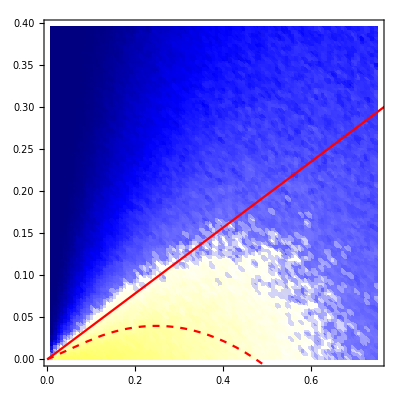

```mathematica
picPDDnpulseα005=Module[{colorfun,fs=22},
colorfun[x_]:=Module[{z=2-2^(1-x),ts=1.5,t0=1.},Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}]];
Show[
ListDensityPlot[
Flatten[scanPDDnpulseα005,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
FrameLabel->{{MaTeX["\\eta",FontSize->fs],None},{None,MaTeX["\\phi_\\mathrm{SB}",FontSize->fs]}},RotateLabel->False,
PlotLegends->BarLegend[{colorfun,{0,10}},{0,0.5,1,1.5,2,3,4},LegendMarkerSize->300,
LegendLabel->MaTeX["\\Phi_{\\mathrm{SB}}/\\phi_{\\mathrm{SB}}",FontSize->16],LabelStyle->Directive[15,FontFamily->"Times"]],
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[{π/8β,π/8(β-(8*0.05) β fpdd[β/0.05])},{β,0,1},PlotStyle->{Red,Directive[Red,Dashed]}]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-noisypulse2.pdf",picPDDnpulseα005]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/mathematica/../img/pdd-noisypulse2.pdf

```mathematica
Module[{η=0.03,αmax=0.25,βmax=0.75,nres=100,dβ,dα,Zn,Xn,Un},
{dα,dβ}={αmax,βmax}/100;
AbsoluteTiming[scanPDDnpulseη003=ParallelTable[{α,β,
Max[Table[
Un=MatrixExp[-ⅈ*RandomOmega[α,β]];
Zn=MatrixExp[-ⅈ (π/2KroneckerProduct[Z,Id]+η RandomOmega[0,1])];
Xn=MatrixExp[-ⅈ (π/2KroneckerProduct[X,Id]+η RandomOmega[0,1])];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{300}]]/β
},{α,0,αmax-dα,dα},{β,dβ,βmax,dβ}];]
]
```

{1323.39,Null}

```mathematica
Export[NotebookDirectory[]<>"scanPDDnpulseη003.mx",scanPDDnpulseη003];
```

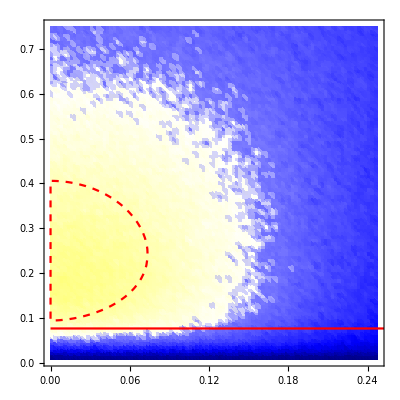

```mathematica
picPDDnpulse2=Module[{colorfun,fs=22},
colorfun[x_]:=Module[{z=2-2^(1-x),ts=1.5,t0=1.},Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}]];
Show[ListDensityPlot[
Flatten[scanPDDnpulseη003,1],
PlotRange->All,PlotRangePadding->0,
ColorFunction->colorfun,ColorFunctionScaling->False,
PlotLegends->BarLegend[{colorfun,{0,10}},{0,0.5,1,1.5,2,3,4},LegendMarkerSize->300,
LegendLabel->MaTeX["\\Phi_{\\mathrm{SB}}/\\phi_{\\mathrm{SB}}",FontSize->16],LabelStyle->Directive[15,FontFamily->"Times"]],
FrameLabel->{{MaTeX["\\phi_{\\mathrm{SB}}",FontSize->fs],None},{None,MaTeX["\\phi_{\\mathrm{B}}",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
RegionPlot[ 
(π/8)(β-8α β fpdd[β/α])≥0.03,
{α,0.0,0.25},{β,0.0,0.75},PlotStyle->None,BoundaryStyle->{Red,Dashed}
],
Plot[8/π*0.03,{x,0,1},PlotStyle->Red]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-noisypulse1.pdf",picPDDnpulse2]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/mathematica/../img/pdd-noisypulse1.pdf

```mathematica
N[π/(4 √2)]
```

0.55536

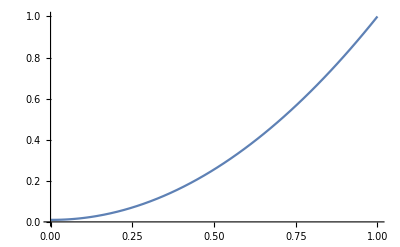

```mathematica
Plot[t^2-b t+b/.b->0.01,{t,0,1}]
```

```mathematica
Module[{α=0,βmax=0.1,dβ,θmax=0.15,dθ,U},
dθ=θmax/100;
dβ=βmax/100;
AbsoluteTiming[scanPDDrutbc=ParallelTable[{β,θ,
Max[Table[
U=RandomUniRot[θ];
ErrorPhase[
MatrixLog[PDDn[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.U,X.U]]],{100}]]/β
},{θ,0,θmax-dθ,dθ},{β,dβ,βmax,dβ}];]
]
```

{200.452,Null}

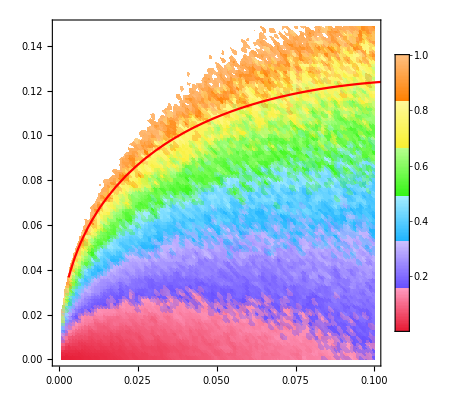

```mathematica
Module[{colorfun,fs=22,ts=1.5,t0=1,α=0.0},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
Show[ListDensityPlot[
Flatten[scanPDDrutbc,1],
PlotRange->{0,1},PlotRangePadding->0,
ColorFunction->"BrightBands",ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\alpha="<>ToString[α],FontSize->fs],Scaled[{1,1}],{1,1},Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\theta",FontSize->fs],None},{None,MaTeX["\\beta",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[(1-32α^2)^(1/4)Sqrt[β/2]-β,{β,0,0.15},PlotStyle->Red]
]]
```

```mathematica
PDDn[U_,Z_,X_]:=-KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U.KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U;
```

```mathematica
CDD2n[U_,Z_,X_]:=PDDn[PDDn[U,Z,X],Z,X];
```

```mathematica
CDD3n[U_,Z_,X_]:=PDDn[CDD2n[U,Z,X],Z,X];
```

```mathematica
Module[{α=0.0,βmax=0.1,dβ,θmax,dθ},
θmax=βmax/8;
dθ=θmax/100;
dβ=βmax/100;
AbsoluteTiming[scanCDD2rutb=ParallelTable[{β,θ,
Max[Table[ErrorPhase[
MatrixLog[CDD2n[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.RandomUniRot[θ],X.RandomUniRot[θ]]]],{100}]]/β
},{θ,0,θmax-dθ,dθ},{β,dβ,βmax,dβ}];]
]
```

{222.289,Null}

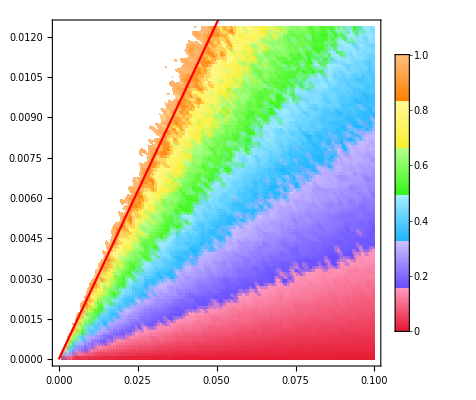

```mathematica
Module[{colorfun,fs=22,ts=1.5,t0=1,θ=0.1},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
Show[
ListDensityPlot[
Flatten[scanCDD2rutb,1],
PlotRange->{0,1},PlotRangePadding->0,
ColorFunction->"BrightBands",ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\alpha=0.05",FontSize->fs],Scaled[{0.9,0.95}],Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\theta",FontSize->fs],None},{None,MaTeX["\\beta",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[x/4,{x,0,1},PlotStyle->Red]
]]
```

```mathematica
Module[{α=0.0,βmax=0.1,dβ,θmax,dθ},
θmax=βmax/8;
dθ=θmax/100;
dβ=βmax/100;
AbsoluteTiming[scanCDD3rutb=ParallelTable[{β,θ,
Max[Table[ErrorPhase[
MatrixLog[CDD3n[ MatrixExp[-ⅈ*RandomOmega[α,β]] ,Z.RandomUniRot[θ],X.RandomUniRot[θ]]]],{100}]]/β
},{θ,0,θmax-dθ,dθ},{β,dβ,βmax,dβ}];]
]
```

{233.308,Null}

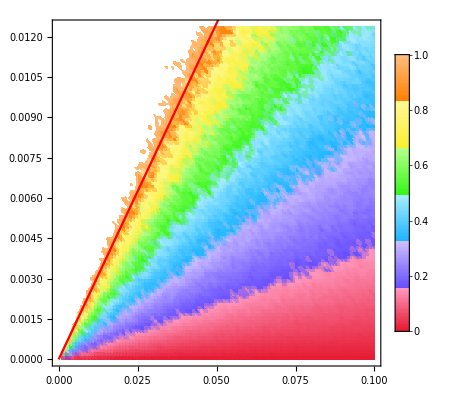

```mathematica
pcdd3=Module[{colorfun,fs=22,ts=1.5,t0=1,α=0.},
colorfun[z_]:=Piecewise[{{Darker[Blue,z-ts],z≥ ts},{Lighter[Blue,ts-z],t0≤ z<ts},{Lighter[Yellow,z],0<=z<t0}}];
Show[
ListDensityPlot[
Flatten[scanCDD3rutb,1],
PlotRange->{0,1},PlotRangePadding->0,
ColorFunction->"BrightBands",ColorFunctionScaling->False,
Epilog->Text[MaTeX["\\alpha="<>ToString[α],FontSize->fs],Scaled[{1,1}],{1,1},Background->White],
PlotLegends->Automatic,
FrameLabel->{{MaTeX["\\theta",FontSize->fs],None},{None,MaTeX["\\beta",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[x/4,{x,0,1},PlotStyle->Red]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/pdd-gatedep-thres.pdf",ppddgatdep]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/pdd-gatedep-thres.pdf

```mathematica
Export[NotebookDirectory[]<>"../img/cdd-gatedep-thres.pdf",pcdd3]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/cdd-gatedep-thres.pdf

```mathematica
X
```

{{0,1},{1,0}}

```mathematica
π/2 KroneckerProduct[X,Id]+0.1 RandomOmega[0.1,0.1]
```

{{0.000716947+0. ⅈ,0.00143719-0.00605903 ⅈ,1.56984-0.00267134 ⅈ,-0.000734634-0.00346279 ⅈ},{0.00143719+0.00605903 ⅈ,-0.00931301+0. ⅈ,-0.00226354-0.0010571 ⅈ,1.57452-0.00211372 ⅈ},{1.56984+0.00267134 ⅈ,-0.00226354+0.0010571 ⅈ,0.0164473+0. ⅈ,-0.00200304-0.00419125 ⅈ},{-0.000734634+0.00346279 ⅈ,1.57452+0.00211372 ⅈ,-0.00200304+0.00419125 ⅈ,-0.00785124+0. ⅈ}}

```mathematica
(* PDD with finite-width pulse *)
```

```mathematica
Module[{α=0.01,β=0.01,W,x=1,Un,Xn,Zn},
Max[Table[
W=RandomOmega[α,β];
Un=MatrixExp[-ⅈ (1-x)W];
Xn=MatrixExp[-ⅈ(π/2 KroneckerProduct[X,Id]+x W)];
Zn=MatrixExp[-ⅈ(π/2 KroneckerProduct[Z,Id]+x W)];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{10000}]]/β
]
```

1.76498

```mathematica
N[4√2/π]
```

1.80063

```mathematica
Module[{α=0.0,βmax=0.2,dβ=0.002,xmax=0.2,dx=0.002,W,Xn,Zn,Un},
AbsoluteTiming[
scanPDDfinite=ParallelTable[{β,x,
Max[Table[
W=RandomOmega[α,β];
Un=MatrixExp[-ⅈ (1-x)W];
Xn=MatrixExp[-ⅈ(π/2 KroneckerProduct[X,Id]+x W)];
Zn=MatrixExp[-ⅈ(π/2 KroneckerProduct[Z,Id]+x W)];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{200}]]/β},
{x,0,xmax-dx,dx},{β,dβ,βmax,dβ}];]
]
```

{498.474,Null}

```mathematica
π/8.
```

0.392699

```mathematica
Length[scanPDDfinite]
```

2

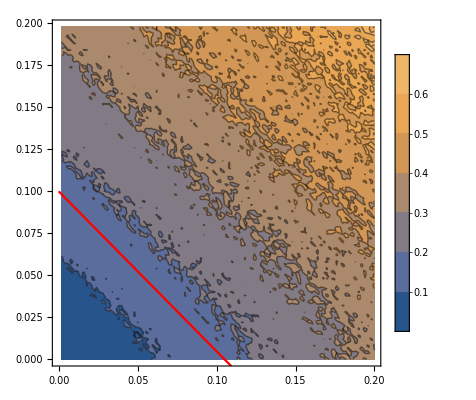

```mathematica
figPDDfinite=Module[{colorfun,fs=22,ts=1.5,t0=1,α=0.},
colorfun="PigeonTones";
Show[
ListContourPlot[
Flatten[scanPDDfinite,1],
PlotRange->{0,1},PlotRangePadding->0,
ColorFunctionScaling->False,
PlotLegends->Automatic,
FrameLabel->{{MaTeX["x",FontSize->fs],None},{None,MaTeX["\\beta",FontSize->fs]}},RotateLabel->False,
FrameTicks->Automatic,FrameStyle->Directive[16,FontFamily->"Times"],
ImageSize->400],
Plot[0.1-π/3.3 x,{x,0,1},PlotStyle->Red]
]]
```

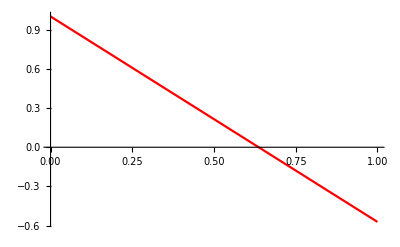

```mathematica
Plot[1-π/2 x,{x,0,1},PlotStyle->Red]
```

```mathematica
scanPDDfinite[[1]]
```

{{0.002,0.,0.00359922},{0.004,0.,0.00599331},{0.006,0.,0.0101232},{0.008,0.,0.0122051},{0.01,0.,0.0173126},{0.012,0.,0.0209727},{0.014,0.,0.0242674},{0.016,0.,0.025196},{0.018,0.,0.0268369},{0.02,0.,0.0288708},{0.022,0.,0.0373806},{0.024,0.,0.0392479},{0.026,0.,0.0449422},{0.028,0.,0.0490714},{0.03,0.,0.046352},{0.032,0.,0.0510019},{0.034,0.,0.0563136},{0.036,0.,0.0604805},{0.038,0.,0.0593775},{0.04,0.,0.0678794},{0.042,0.,0.0682055},{0.044,0.,0.0671668},{0.046,0.,0.0719385},{0.048,0.,0.0785666},{0.05,0.,0.0849738},{0.052,0.,0.0768566},{0.054,0.,0.0967548},{0.056,0.,0.0883039},{0.058,0.,0.091984},{0.06,0.,0.105287},{0.062,0.,0.108153},{0.064,0.,0.10792},{0.066,0.,0.107243},{0.068,0.,0.125671},{0.07,0.,0.119763},{0.072,0.,0.111688},{0.074,0.,0.128184},{0.076,0.,0.110311},{0.078,0.,0.137039},{0.08,0.,0.110678},{0.082,0.,0.126853},{0.084,0.,0.134583},{0.086,0.,0.138408},{0.088,0.,0.142257},{0.09,0.,0.164132},{0.092,0.,0.169353},{0.094,0.,0.157365},{0.096,0.,0.163885},{0.098,0.,0.14743},{0.1,0.,0.182572},{0.102,0.,0.17124},{0.104,0.,0.178913},{0.106,0.,0.175194},{0.108,0.,0.171066},{0.11,0.,0.182252},{0.112,0.,0.173053},{0.114,0.,0.21755},{0.116,0.,0.188114},{0.118,0.,0.190177},{0.12,0.,0.196618},{0.122,0.,0.194318},{0.124,0.,0.210788},{0.126,0.,0.209526},{0.128,0.,0.209013},{0.13,0.,0.212913},{0.132,0.,0.200981},{0.134,0.,0.220799},{0.136,0.,0.246514},{0.138,0.,0.230356},{0.14,0.,0.225205},{0.142,0.,0.214236},{0.144,0.,0.220657},{0.146,0.,0.231674},{0.148,0.,0.280537},{0.15,0.,0.263602},{0.152,0.,0.252641},{0.154,0.,0.298992},{0.156,0.,0.230484},{0.158,0.,0.245724},{0.16,0.,0.284249},{0.162,0.,0.283898},{0.164,0.,0.236999},{0.166,0.,0.265904},{0.168,0.,0.276603},{0.17,0.,0.324744},{0.172,0.,0.289116},{0.174,0.,0.287635},{0.176,0.,0.29861},{0.178,0.,0.298868},{0.18,0.,0.271621},{0.182,0.,0.299366},{0.184,0.,0.311131},{0.186,0.,0.284418},{0.188,0.,0.325844},{0.19,0.,0.355759},{0.192,0.,0.310287},{0.194,0.,0.276746},{0.196,0.,0.3213},{0.198,0.,0.319671},{0.2,0.,0.305439}}

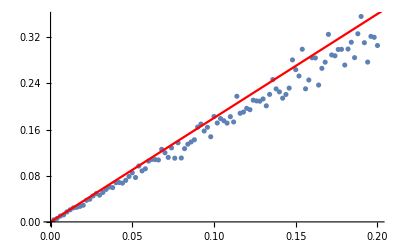

```mathematica
Show[ListPlot[
Transpose[Transpose[scanPDDfinite[[1]]][[{1,3}]]]],
Plot[4/π √2 r,{r,0,1},PlotStyle->Red]]
```

```mathematica
Module[{B,n,Ω,Ex,Ey,Ez,Ei,α=0.01,β=0.01,r,
XI=KroneckerProduct[X,Id],
YI=KroneckerProduct[Y,Id],
ZI=KroneckerProduct[Z,Id]},
B[0]=α RandomBath0[2];
{B[1],B[2],B[3]}=Table[RandomHermitian[2],{3}];
Ω=Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
n=Norm[Ω];
{B[1],B[2],B[3]}=(β/n){B[1],B[2],B[3]};
Ω=Sum[KroneckerProduct[σ[i],B[i]],{i,0,3}];
Ez=KroneckerProduct[σ[0],B[0]]-2/π KroneckerProduct[σ[1],B[2]]
+2/π KroneckerProduct[σ[2],B[1]]+KroneckerProduct[σ[3],B[3]];
Ey=KroneckerProduct[σ[0],B[0]]-KroneckerProduct[σ[1],B[1]]
+2/π KroneckerProduct[σ[2],B[3]]+2/π KroneckerProduct[σ[3],B[2]];
Ex=KroneckerProduct[σ[0],B[0]]+2/π KroneckerProduct[σ[1],B[2]]
+2/π KroneckerProduct[σ[2],B[1]]-KroneckerProduct[σ[3],B[3]];
Ei=KroneckerProduct[σ[0],B[0]]+KroneckerProduct[σ[1],B[1]]
+2/π KroneckerProduct[σ[2],B[3]]-2/π KroneckerProduct[σ[3],B[2]];

Table[{r,Norm[
MatrixLog[MatrixExp[-ⅈ π/2 ZI].MatrixExp[ⅈ(π/2 ZI- r*(XI.Ω.XI))]]+ⅈ r Ex
]},{r,0,0.1,0.002}]
]
```

{{0.,0.},{0.002,1.36184×10^-10},{0.004,5.44738×10^-10},{0.006,1.22566×10^-9},{0.008,2.17894×10^-9},{0.01,3.4046×10^-9},{0.012,4.90261×10^-9},{0.014,6.67299×10^-9},{0.016,8.71573×10^-9},{0.018,1.10308×10^-8},{0.02,1.36183×10^-8},{0.022,1.64781×10^-8},{0.024,1.96103×10^-8},{0.026,2.30148×10^-8},{0.028,2.66917×10^-8},{0.03,3.0641×10^-8},{0.032,3.48626×10^-8},{0.034,3.93566×10^-8},{0.036,4.41229×10^-8},{0.038,4.91615×10^-8},{0.04,5.44725×10^-8},{0.042,6.00559×10^-8},{0.044,6.59116×10^-8},{0.046,7.20397×10^-8},{0.048,7.84401×10^-8},{0.05,8.51128×10^-8},{0.052,9.20579×10^-8},{0.054,9.92753×10^-8},{0.056,1.06765×10^-7},{0.058,1.14527×10^-7},{0.06,1.22562×10^-7},{0.062,1.30869×10^-7},{0.064,1.39448×10^-7},{0.066,1.48299×10^-7},{0.068,1.57423×10^-7},{0.07,1.66819×10^-7},{0.072,1.76488×10^-7},{0.074,1.86428×10^-7},{0.076,1.96642×10^-7},{0.078,2.07127×10^-7},{0.08,2.17885×10^-7},{0.082,2.28915×10^-7},{0.084,2.40217×10^-7},{0.086,2.51792×10^-7},{0.088,2.63639×10^-7},{0.09,2.75759×10^-7},{0.092,2.88151×10^-7},{0.094,3.00815×10^-7},{0.096,3.13751×10^-7},{0.098,3.2696×10^-7},{0.1,3.40441×10^-7}}

```mathematica
Ωrand=RandomOmega[0.1,0.1];
```

```mathematica
RandomOmega[a_,b_,n_:2]:=a KroneckerProduct[σ[0],RandomBath0[w]]+b Normalize[Sum[KroneckerProduct[σ[i],RandomHermitian[n]],{i,1,3}],Norm]
```

```mathematica
TcpNorm[ⅈ MatrixLog[ⅈ KroneckerProduct[X,Id].MatrixExp[(-ⅈ π)/2 KroneckerProduct[X,Id]-ⅈ  Ωrand]]]
```

{0.100544,0.0683266}

```mathematica
(* Let B1=B3=0 *)
```

```mathematica
Module[{α=0.1,β=0.01,xmax=0.2,dx=0.002,W,B,n,Xn,Zn,Un},
AbsoluteTiming[
scanPDDfinite2=ParallelTable[{x,
Max[Table[
B[0]=α RandomBath0[2];
B[1]=0Id;
B[2]=RandomHermitian[2];
B[3]=0Id;
W=Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
n=Norm[W];
{B[1],B[2],B[3]}=(β/n){B[1],B[2],B[3]};
W=Sum[KroneckerProduct[σ[i],B[i]],{i,0,3}];
Un=MatrixExp[-ⅈ (1-x)W];
Xn=MatrixExp[-ⅈ(π/2 KroneckerProduct[X,Id]+x W)];
Zn=MatrixExp[-ⅈ(π/2 KroneckerProduct[Z,Id]+x W)];
ErrorPhase[MatrixLog[PDDn[Un,Zn,Xn]]],{500}]]/β},
{x,0,xmax-dx,dx}];]
]
```

{13.1085,Null}

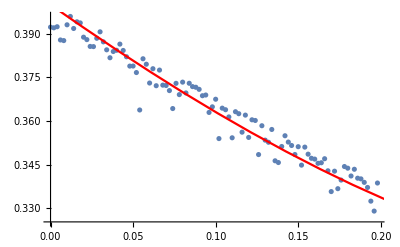

```mathematica
Show[ListPlot[scanPDDfinite2],
Plot[0.4 √((2/π r)^2+(1-r)^2+r^2),{r,0,1},PlotStyle->Red]]
```